```mathematica
list=FileNames["*.m",NotebookDirectory[]][[;;]]
listdat=FileNames["*.dat",NotebookDirectory[]][[;;]];
```

{/home/pier/Desktop/git/membranes/membrane/gaussian_curvature.m,/home/pier/Desktop/git/membranes/membrane/mean_curvature.m}

## Visualizing geometry

```mathematica
resize[ll_]:=Module[{max,min},
max=Max[ll[[;;,1]]];
min=Min[ll[[;;,1]]];
Sort[Table[{(-min+ll[[i,1]])/(max-min),ll[[i,2]]},{i,Length@ll}]]
]
geometry1=Import[NotebookDirectory[]<>"mesh/geometries/dumbbell_6.dat"]//Chop;
geometry2=Import[NotebookDirectory[]<>"mesh/geometries/dumbbell_7.dat"]//Chop;
geometry3=Import[NotebookDirectory[]<>"mesh/geometries/sphere_2.dat"]//Chop;
```

```mathematica
Sort/@DeleteDuplicates/@Map[Length,#,{2}]&@{geometry1,geometry2,geometry3}
```

{{15,16,17,18,19,20,21},{16,17,18,19,20,21},{16,17,18,19,20,21}}

```mathematica
g1H=resize[geometry1[[;;,{2,8}]]];
g1KG=resize[geometry1[[;;,{2,9}]]];
g2H=resize[geometry2[[;;,{2,8}]]];
g2KG=resize[geometry2[[;;,{2,9}]]];
g3H=resize[geometry3[[;;,{2,8}]]];
g3KG=resize[geometry3[[;;,{2,9}]]];
```

```mathematica
<<MaTeX`
```

```mathematica
zcoord=Show[MaTeX["z"],ImageSize->30];
h2=Show[MaTeX["H^2 [A^{-1}]"],ImageSize->150];
kg=Show[MaTeX["K_G [A^{-1}]"],ImageSize->150];
```

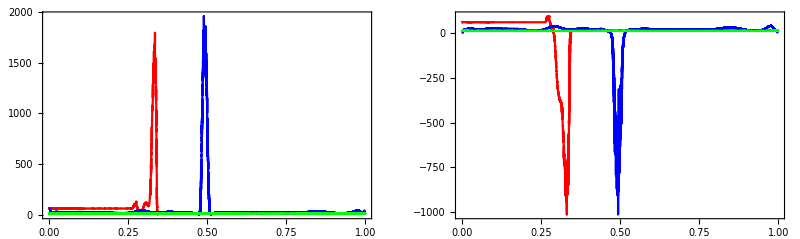

```mathematica
graph1=GraphicsRow[{
ListPlot[{g1H,g2H[[30;;-30]],g3H},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,Green},Frame->True,Axes->False,FrameStyle->Large,FrameLabel->{zcoord,h2}],
ListPlot[{g1KG,g2KG[[30;;-30]],g3KG},PlotRange->All,Joined->True,PlotStyle->{Red,Blue,Green},Frame->True,Axes->False,FrameStyle->Large,FrameLabel->{zcoord,kg}]
},
ImageSize->Full]
```

```mathematica
Export[ToString[NotebookDirectory[]]<>"../../curvatures.pdf",graph1,ImageSize->2000]
```

/home/pier/Desktop/git/membranes/membrane/../../curvatures.pdf

3D plots

```mathematica
GraphicsRow[{Graphics3D[{EdgeForm[Transparent],Import[list[[1]]]},Boxed->False,ImageSize->500,PlotRange->All],Graphics3D[{EdgeForm[Transparent],Import[list[[-1]]]},Boxed->False,ImageSize->500,PlotRange->All]},ImageSize->1000]
```

## Visualizing data

```mathematica
Graphics3D[{EdgeForm[Transparent],Import[list[[2]]]},Boxed->False,ImageSize->500,PlotRange->All]
```

-Graphics3D-

Worldline

```mathematica
w2d=Import[listdat[[-2]]]//Select[#,Length[#]==3&]&;
w3d=Import[listdat[[-1]]]//Select[#,Length[#]==4&]&;
```

```mathematica
timelist=w2d[[;;,3]]//DeleteDuplicates;
```

```mathematica
ww2d=Table[Select[w2d,#[[3]]==timelist[[i]]&],{i,Length@timelist}];
ww3d=Table[Select[w3d,#[[4]]==timelist[[i]]&],{i,Length@timelist}];
```

```mathematica
w2dd=Table[Table[{ww2d[[i,j,1]],ww2d[[i,j,2]],ww2d[[i,j,3]],Log@ww2d[[i,j,3]]},{j,Length@ww2d[[i]]}],{i,Length@ww2d}];
w3dd=Table[Table[{ww3d[[i,j,1]],ww3d[[i,j,2]],ww3d[[i,j,3]],ww3d[[i,j,4]],Log@ww3d[[i,j,4]]},{j,Length@ww3d[[i]]}],{i,Length@ww3d}];
```

```mathematica
(*w2dd[[5;;-390,;;,{1,2,4}]]//ListPointPlot3D*)
```

```mathematica
Plot3D[{√(1-(x/2)^2-(y/3)^2),-√(1-(x/2)^2-(y/3)^2)},{x,-2,2},{y,-3,3},BoxRatios->{1, 1, 1},PlotRange->{{-3,3},{-3,3},{-3,3}},Mesh->None,PlotStyle->{Red,Red},Boxed->False,Axes->False,ImageSize->1000]
```

-Graphics3D-

## Debugging

```mathematica
p=geometry;Length@p
```

29411

```mathematica
Graphics3D[{Arrowheads[.01],Table[Arrow[{p[[i,{2,3,4}]],p[[i,{2,3,4}]]+.2p[[i,{10,11,12}]]}],{i,1,Length@p,100}]}]
```

-Graphics3D-

```mathematica
Show[{Graphics3D[{Arrowheads[.01],Table[Arrow[{p[[i,{2,3,4}]],p[[i,{2,3,4}]]+.1p[[i,{10,11,12}]]}],{i,1,Length@p,1000}]}],
Graphics3D[{EdgeForm[Transparent],FaceForm[{Pink,Opacity[0.8]}],Import[list[[1]]]}]},ImageSize->600,PlotRange->{-1,1}]
```

-Graphics3D-